# The Walking Dead : Malaria Edition

## Functions

```mathematica
SetDirectory[NotebookDirectory[]]
(*Movement Kernels*)
CalculateEuclideanDistances[coordinatesSet_]:=Table[N[EuclideanDistance[coordinatesSet[[i]],#]]&/@coordinatesSet,{i,1,coordinatesSet//Length }]
CalculateInverseLinearKernelMigrationProbabilities[distancesMatrix_,nonMigratoryForce_]:=N[(#/Total[#])]&/@ReplaceAll[1/distancesMatrix//Quiet,ComplexInfinity->nonMigratoryForce]
ExponentialKernel[λ_,distance_]:=λ*ⅇ^(-λ*distance)
(*Markov*)
CalculateMarkovSteadyState[migrationProbabilities_]:=Module[{initialState,markov,markovPDF},
initialState=ConstantArray[0,migrationProbabilities//Length]//ReplacePart[#,1->1]&;
markov=DiscreteMarkovProcess[initialState,migrationProbabilities];
markovPDF=PDF[StationaryDistribution[markov],#]&/@Range[markov[[1]]//Length];
markovPDF
]
(*Networks Plot*)
edgeshape[e_,___]:={Arrowheads[{{.0075,.5}}],Arrow[e]}
Options[EdgesStyleList]:={LineThickness->.004,VariableStyle->"Both"}
EdgesStyleList[vertexSyllableList_,OptionsPattern[]]:=Switch[OptionValue[VariableStyle],
"LineColor",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Opacity[1*vertexSyllableList[[i]][[2]]+.025],Thickness[OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],
"LineWidth",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Opacity[.5],Blue,Thickness[vertexSyllableList[[i]][[2]]*OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],
"Both",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Opacity[.75*vertexSyllableList[[i]][[2]]+.05],Thickness[vertexSyllableList[[i]][[2]]*OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],_,Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Thickness[OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}]]
VertexNumberToVertexSyllable[syllables_,fixedEdgesList_]:=Table[DirectedEdge[syllables[[fixedEdgesList[[index]][[1]][[1]]]],syllables[[fixedEdgesList[[index]][[1]][[2]]]]->fixedEdgesList[[index]][[2]]]//N,{index,1,Length[fixedEdgesList]}]
Options[GraphTransitionsFrequenciesWithMax]:={ImagePadding->None,Background->White,VertexStyle->Automatic,VertexCoordinates->Automatic,LineThickness->.0005,VariableStyle->"Both",GraphLayout->Automatic,Frame->False,FrameStyle->Thick,ImageSize->Automatic,VertexSize->.5,PlotTheme->"LakeNetwork",EdgeShapeFunction->edgeshape,VertexLabelStyle->{Italic},Prolog->{},Epilog->{},VertexShape->Automatic}
GraphTransitionsFrequenciesWithMax[frequenciesOutput_,max_,OptionsPattern[]]:=Module[{frequencies,syllables,edges,fixedEdgesList,vertexSyllableList,normalizedVertexSyllableList,edgesStyleList,links},frequencies=frequenciesOutput[[1]];
syllables=frequenciesOutput[[2]];
edges=Table[DirectedEdge[i,j]->frequencies[[i,j]],{i,Length[syllables]},{j,Length[syllables]}]//Flatten;
fixedEdgesList=DeleteCases[edges,DirectedEdge[_,_]->0];
vertexSyllableList=VertexNumberToVertexSyllable[frequenciesOutput[[2]],fixedEdgesList];
normalizedVertexSyllableList=(DirectedEdge[#[[1]],#[[2]][[1]]]->#[[2]][[2]]/max&)/@vertexSyllableList;
edgesStyleList=EdgesStyleList[normalizedVertexSyllableList,LineThickness->OptionValue[LineThickness],VariableStyle->OptionValue[VariableStyle]];
links=DirectedEdge[#[[1]],#[[2,1]]]&/@vertexSyllableList;
Graph[syllables,links,
EdgeWeight->vertexSyllableList[[All,2,2]],
VertexStyle->OptionValue[VertexStyle],
EdgeStyle->edgesStyleList,
VertexCoordinates->OptionValue[VertexCoordinates],
ImageSize->OptionValue[ImageSize],
GraphLayout->OptionValue[GraphLayout],
EdgeShapeFunction->OptionValue[EdgeShapeFunction],
VertexShape->OptionValue[VertexShape],
VertexSize->OptionValue[VertexSize],
Frame->OptionValue[Frame],
FrameStyle->OptionValue[FrameStyle],
VertexLabelStyle->OptionValue[VertexLabelStyle],
VertexLabels->Placed["Name",Center],
EdgeLabels->Table[links[[i]]->Placed[fixedEdgesList[[All,2]][[i]],Tooltip],{i,Length[links]}],
Prolog->OptionValue[Prolog],
Epilog->OptionValue[Epilog],
Background->OptionValue[Background],
ImagePadding->OptionValue[ImagePadding],
PerformanceGoal->"Speed"
]
]
(*Plots Styles*)
Themes`AddThemeRules["LakeMatrixPlot"
,AspectRatio->1
,AxesStyle->Directive[Gray,Opacity[.5],Dashed]
,ColorFunction->ColorData[{"LakeColors","Reverse"}]
,Frame->True
,FrameStyle->Directive[Gray,Thick]
,FrameTicks->False
,ImageSize->250
,PlotRangePadding->0
]
Themes`AddThemeRules["LakeNetwork",
,EdgeShapeFunction->edgeshape2
,Epilog->Riffle[ConstantArray[Directive[Opacity[1],Lighter[Purple,.45],EdgeForm[Directive[Opacity[.75],Thickness[.005]]]],sampledCoordinates//Length],(Disk[#,.25]&/@sampledCoordinates)]
,ImageSize -> 500
,ImagePadding->25
,LineThickness -> .0075
,VariableStyle->"Both"
,VertexCoordinates ->sampledCoordinates
,VertexSize ->.01
,VertexLabelStyle->.001
]
(*USES GLOBALS!*)
GraphPlotWrapper[migrationMatrix_,max_,vertexSize_,vertexStyle_]:= GraphTransitionsFrequenciesWithMax[
  {
migrationMatrix,
ToString /@ Range[Length[migrationMatrix]]
   }, max
,EdgeShapeFunction->edgeshape2
,ImagePadding->0
,ImageSize->imageSize
,LineThickness->lineThickness
,VariableStyle->"Both"
,VertexCoordinates->sampledCoordinates
,VertexSize -> vertexSize
,VertexStyle->vertexStyle
,VertexLabelStyle->.0001
  ]
```

/Users/sanchez.hmsc/Documents/GitHub/MoNeT/Dev/HectorSanchez/WalkingDead

LakeMatrixPlot

LakeNetwork

## Inputs

Style

```mathematica
edgeChopThreshold=10^-1.5;
edgeshape2[e_,___]:={Arrowheads[{{.000000001,1}}],Arrow[e]}
lineThickness=.0005;
imageSize=250;
```

Geo - Setting

```mathematica
{citiesNumber,networkDimension,distance}={{500,50},4,25};
(**)
movementProbabilitiesVector=If[networkDimension>1,ConstantArray[0,networkDimension]//ReplacePart[#,{2->1,3->0}]&,ConstantArray[0,networkDimension]//ReplacePart[#,{1->1}]&];
penalizationsMatrix=Table[RotateRight[movementProbabilitiesVector,i-1],{i,1,networkDimension}];
MatrixForm[penalizationsMatrix]
```

(0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0)

Random Walks

```mathematica
{chainsSteps,chainsNumber}={20,30};
```

## Spatial Setting

2 D - Grid

```mathematica
citiesSqrt=Range[0,citiesNumber[[1]],citiesNumber[[2]]];
sampledCoordinates=Tuples[citiesSqrt,2];
clusteredCoordinates=FindClusters[sampledCoordinates,Method->"NeighborhoodContraction"];
euclideanDistances=CalculateEuclideanDistances[sampledCoordinates];
(**)
colors=Reverse[ColorData["BrightBands",#]&/@Range[0,1,1/(Length[clusteredCoordinates])]]//Flatten//RandomSample;
gridCoordinatesPlot=ListPlot[clusteredCoordinates//Flatten[#,1]&
,AspectRatio->1
,AxesStyle->Directive[Gray,Opacity[.5],Dashed]
,GridLines->None
,GridLinesStyle->Directive[Gray,Opacity[.5],Dashed]
,ImageSize->250
,PlotRangePadding->.5
,PlotStyle->Directive[Purple,EdgeStyle[Black],Opacity[.75],PointSize[.02]]
,Frame->True
,FrameStyle->Directive[Gray,Thick]
,FrameTicks->False
,FrameTicksStyle->15
];
matrixDistancesPlot=MatrixPlot[Sort/@euclideanDistances,PlotTheme->"LakeMatrixPlot"];
Grid[{{gridCoordinatesPlot,matrixDistancesPlot}}];
```

Movement Kernel

### Inverse-Linear Kernel

```mathematica
(*migrationProbabilities=CalculateInverseLinearKernelMigrationProbabilities[euclideanDistances,0];
(**)
matrixMigrationPlot=MatrixPlot[Sort/@migrationProbabilities,PlotTheme->"LakeMatrixPlot"];
colorsType=Reverse[ColorData["LakeColors",#]&/@Range[0,1,1/networkDimension]];
stylesSwatchType=Directive[Opacity[1],Lighter[Purple,.45],EdgeForm[Directive[Opacity[.75],Thickness[.005]]]]&/@Range[networkDimension];
stylesListType=(ToString[#]->stylesSwatchType[[1]])&/@Range[migrationProbabilities//Length];
originalMap=GraphPlotWrapper[
Chop[migrationProbabilities//LowerTriangularize,edgeChopThreshold],.1,
(#->.5)&/@(ToString/@Range[migrationProbabilities//Length]),
stylesListType
];*)
```

### Exponential Kernel

```mathematica
migrationProbabilities=(#/Total[#])&/@ReplacePart[ExponentialKernel[0.01848777,#]&/@euclideanDistances,{i_,i_}->0];
(**)
matrixMigrationPlot=MatrixPlot[Sort/@migrationProbabilities,PlotTheme->"LakeMatrixPlot"];
colorsType=Reverse[ColorData["LakeColors",#]&/@Range[0,1,1/networkDimension]];
stylesSwatchType=Directive[Opacity[1],Lighter[Purple,.45],EdgeForm[Directive[Opacity[.75],Thickness[.005]]]]&/@Range[networkDimension];
stylesListType=(ToString[#]->stylesSwatchType[[1]])&/@Range[migrationProbabilities//Length];
originalMap=GraphPlotWrapper[
Chop[migrationProbabilities//LowerTriangularize,.05*edgeChopThreshold],.1,
(#->.5)&/@(ToString/@Range[migrationProbabilities//Length]),
stylesListType
];
```

Markov Baseline

```mathematica
baselineMarkovSS=CalculateMarkovSteadyState[migrationProbabilities];
(**)
colorsType=Reverse[ColorData["LakeColors",#]&/@Range[0,1,1/networkDimension]];
stylesSwatchType=Directive[Opacity[1],Lighter[Purple,.45],EdgeForm[Directive[Opacity[.75],Thickness[.005]]]]&/@Range[networkDimension];
stylesListType=(ToString[#]->stylesSwatchType[[1]])&/@Range[migrationProbabilities//Length];
markovBaseline=GraphPlotWrapper[
Chop[migrationProbabilities//LowerTriangularize,.05*edgeChopThreshold],.1,
Thread[VertexList[originalMap ]->.25*Log[.5+7.5*Rescale[baselineMarkovSS]]],
stylesListType
];
```

## Network Dimensionality

Dimension

```mathematica
cityType=RandomChoice[Range[networkDimension],sampledCoordinates//Length]
dimensionalPenalizationsMask=Table[penalizationsMatrix[[i,#]]&/@cityType,{i,cityType}];
migrationDimensionalMatrix=(#/Total[#])&/@(dimensionalPenalizationsMask*migrationProbabilities);
(**)
matrixPenalizationsPlot=MatrixPlot[Sort/@dimensionalPenalizationsMask,PlotTheme->"LakeMatrixPlot"];
matrixDimensionalPlot=MatrixPlot[Sort/@migrationDimensionalMatrix,PlotTheme->"LakeMatrixPlot"];
```

{3,3,3,2,2,2,4,1,1,4,3,1,4,2,4,2,1,2,4,2,3,4,3,1,2,3,4,2,2,4,2,4,2,2,4,4,1,2,1,1,2,3,1,4,1,1,1,4,3,4,3,4,2,1,2,2,3,1,1,2,2,1,1,2,4,4,3,4,1,1,3,2,4,2,3,3,2,4,1,2,2,1,4,1,4,3,4,1,4,1,4,3,3,1,3,1,2,2,1,1,1,1,1,2,2,1,2,4,2,3,4,2,1,2,2,1,4,4,1,1,3}

Markov Dimensional Network

```mathematica
markovPDF=CalculateMarkovSteadyState[migrationDimensionalMatrix];
(**)
colorsType=Reverse[ColorData["LakeColors",#]&/@Range[0,1,1/networkDimension]];
stylesSwatchType=Directive[Opacity[1],colorsType[[#]],EdgeForm[Directive[Opacity[.75],Thickness[.005]]]]&/@Range[networkDimension];
stylesListType=(ToString[#[[1]]]->stylesSwatchType[[#[[2]]]])&/@Transpose[{Range[cityType//Length],cityType}];
markovDimensional=GraphPlotWrapper[
Chop[migrationDimensionalMatrix//LowerTriangularize,edgeChopThreshold],.1,
Thread[VertexList[originalMap ]->.25*Log[0+7.5*Rescale[markovPDF]]],
stylesListType
];
```

Markov Dimensional Difference

```mathematica
colorsType=Reverse[ColorData["LakeColors",#]&/@Range[0,1,1/networkDimension]];
stylesSwatchType=Directive[Opacity[1],colorsType[[#]],EdgeForm[Directive[Opacity[.75],Thickness[.005]]]]&/@Range[networkDimension];
stylesListType=(ToString[#[[1]]]->stylesSwatchType[[#[[2]]]])&/@Transpose[{Range[cityType//Length],cityType}];
markovDimensionalDifference=GraphPlotWrapper[
Chop[migrationDimensionalMatrix//LowerTriangularize,edgeChopThreshold],.1,
Thread[VertexList[originalMap ]->.25*Log[0+7.5*Rescale[Chop[Abs[baselineMarkovSS-markovPDF]]]]],
stylesListType
];
```

```mathematica
distributionOfDifferences=DistributionChart[baselineMarkovSS-markovPDF
,AspectRatio->1/6
,Axes->{False,True}
,AxesOrigin->{0,0}
,AxesStyle->Directive[Thick,Gray,Opacity[.25]]
,BarOrigin->Right
,BarSpacing->0
,ChartStyle->"LakeColors"
,Frame->False
,FrameTicks->None
,FrameStyle->Directive[Gray,Thin]
,GridLines->None
,ImageSize->imageSize
,PlotRange->{All,All}
,PlotRangePadding->0
];
markovDistributions=SmoothHistogram[{baselineMarkovSS,markovPDF}
,Frame->True
,FrameStyle->Directive[Thick,Gray]
,GridLines->Automatic
,PlotRange->{{0,All},{0,All}}
,PlotStyle->{Directive[Red,Thickness[.01]],Directive[Purple,Thickness[.01]]}
,ImageSize->imageSize
,FrameTicks->{Automatic,None}
];
```

## Attractors/Repellents

Attractors

```mathematica
{attractorScaler,attractorCoverage,attractorDimension}={100,.1,2};
attractorDimensionPositions=Position[cityType,attractorDimension];
sampledAttractors=(Position[cityType,attractorDimension]//Flatten//RandomSample)[[1;;Round[attractorCoverage*Length[attractorDimensionPositions]]]];
```

```mathematica
scaledInProbs=((1+attractorScaler)*migrationDimensionalMatrix[[All,#]])&/@sampledAttractors;
replacedMatrix=ReplacePart[migrationDimensionalMatrix//Transpose,(#[[1]]->#[[2]])&/@Transpose[{sampledAttractors,scaledInProbs}]]//Transpose;
renormalizedMatrix=(#/Total[#])&/@replacedMatrix;
MatrixPlot[Chop[migrationDimensionalMatrix-renormalizedMatrix]];
```

Repellents

```mathematica
{repellentEfficacy,repellentCoverage,repellentDimension}={1,.5,1};
repellentDimensionPositions=Position[cityType,repellentDimension];
sampledRepellents=(repellentDimensionPositions//Flatten//RandomSample)[[1;;Round[repellentCoverage*Length[repellentDimensionPositions]]]];
```

## Killing

```mathematica
{killingScaler,killingCoverage,killingDimension}={100,.2,3};
killingDimensionPositions=Position[cityType,killingDimension];
sampledKilling=(Position[cityType,killingDimension]//Flatten//RandomSample)[[1;;Round[killingCoverage*Length[killingDimensionPositions]]]]
```

{51,110,23,71}

## Random Walks

```mathematica
kernel=migrationDimensionalMatrix;
initialState=ConstantArray[0,kernel//Length]//ReplacePart[#,(RandomSample[Range[kernel//Length]][[1]])->1]&;
markov=DiscreteMarkovProcess[initialState,kernel];
paths=Table[
sim=RandomFunction[markov,{0,chainsSteps}];
path=ToString/@Part[sim["ValueList"],1];
path
,{i,1,chainsNumber}];
paths//Grid
```

69 | 80 | 67 | 68 | 47 | 14 | 3 | 13 | 37 | 28 | 42 | 52 | 40 | 16 | 26 | 48 | 59 | 29 | 95 | 118 | 119
69 | 38 | 49 | 50 | 62 | 61 | 92 | 68 | 24 | 34 | 2 | 15 | 24 | 4 | 57 | 36 | 46 | 56 | 49 | 48 | 59
69 | 14 | 1 | 13 | 24 | 34 | 57 | 68 | 90 | 56 | 57 | 68 | 12 | 14 | 23 | 35 | 58 | 56 | 67 | 68 | 37
69 | 115 | 93 | 83 | 96 | 105 | 51 | 73 | 63 | 60 | 95 | 73 | 103 | 105 | 71 | 85 | 96 | 107 | 95 | 85 | 99
69 | 60 | 71 | 83 | 94 | 97 | 86 | 87 | 99 | 97 | 110 | 85 | 84 | 72 | 95 | 83 | 94 | 104 | 92 | 91 | 106
69 | 61 | 93 | 85 | 84 | 74 | 42 | 19 | 9 | 33 | 21 | 30 | 54 | 20 | 21 | 10 | 88 | 77 | 76 | 66 | 88
69 | 80 | 92 | 111 | 102 | 114 | 92 | 83 | 94 | 104 | 92 | 73 | 84 | 98 | 110 | 65 | 94 | 105 | 93 | 48 | 24
69 | 80 | 67 | 78 | 90 | 80 | 57 | 91 | 82 | 104 | 95 | 118 | 119 | 107 | 95 | 108 | 116 | 112 | 92 | 83 | 82
69 | 80 | 71 | 85 | 84 | 97 | 86 | 85 | 94 | 104 | 93 | 83 | 116 | 105 | 95 | 85 | 96 | 107 | 86 | 52 | 63
69 | 72 | 92 | 91 | 102 | 104 | 93 | 83 | 96 | 98 | 76 | 85 | 84 | 104 | 93 | 91 | 102 | 104 | 93 | 91 | 69
69 | 56 | 57 | 35 | 37 | 14 | 2 | 78 | 101 | 104 | 75 | 50 | 17 | 31 | 42 | 32 | 8 | 20 | 21 | 32 | 43
69 | 81 | 71 | 91 | 47 | 34 | 2 | 13 | 37 | 60 | 49 | 36 | 37 | 25 | 49 | 50 | 8 | 6 | 11 | 19 | 9
69 | 80 | 71 | 83 | 84 | 105 | 95 | 66 | 99 | 55 | 76 | 44 | 88 | 97 | 95 | 85 | 96 | 60 | 71 | 52 | 40
69 | 81 | 92 | 111 | 100 | 80 | 92 | 83 | 103 | 104 | 93 | 85 | 84 | 61 | 86 | 44 | 43 | 31 | 11 | 22 | 43
69 | 72 | 71 | 73 | 84 | 105 | 93 | 83 | 82 | 61 | 51 | 50 | 102 | 112 | 71 | 50 | 70 | 29 | 51 | 52 | 63
69 | 80 | 93 | 66 | 54 | 55 | 51 | 52 | 47 | 38 | 26 | 7 | 8 | 20 | 49 | 52 | 40 | 29 | 21 | 32 | 43
69 | 56 | 67 | 91 | 90 | 112 | 67 | 48 | 70 | 72 | 57 | 48 | 58 | 28 | 49 | 83 | 82 | 114 | 93 | 83 | 94
69 | 80 | 92 | 68 | 79 | 80 | 67 | 68 | 59 | 38 | 51 | 52 | 43 | 53 | 86 | 65 | 96 | 107 | 95 | 83 | 106
69 | 60 | 49 | 73 | 58 | 80 | 92 | 91 | 102 | 105 | 93 | 91 | 90 | 112 | 67 | 36 | 58 | 16 | 3 | 15 | 8
69 | 114 | 92 | 78 | 70 | 61 | 71 | 48 | 79 | 80 | 92 | 68 | 101 | 112 | 67 | 35 | 47 | 28 | 49 | 48 | 37
69 | 72 | 92 | 78 | 69 | 56 | 95 | 83 | 94 | 105 | 95 | 117 | 62 | 60 | 71 | 73 | 62 | 61 | 49 | 50 | 58
69 | 104 | 92 | 91 | 101 | 115 | 92 | 83 | 96 | 97 | 86 | 87 | 99 | 109 | 110 | 108 | 119 | 107 | 121 | 87 | 40
69 | 28 | 26 | 13 | 37 | 25 | 1 | 13 | 12 | 25 | 57 | 89 | 90 | 53 | 76 | 65 | 84 | 72 | 3 | 13 | 24
69 | 29 | 21 | 32 | 43 | 97 | 95 | 108 | 96 | 107 | 86 | 85 | 96 | 107 | 75 | 65 | 43 | 20 | 21 | 44 | 9
69 | 41 | 76 | 22 | 40 | 28 | 49 | 50 | 70 | 80 | 57 | 48 | 24 | 34 | 1 | 15 | 37 | 81 | 92 | 87 | 88
69 | 80 | 67 | 68 | 101 | 114 | 93 | 89 | 90 | 80 | 71 | 83 | 82 | 60 | 49 | 48 | 69 | 72 | 51 | 52 | 63
69 | 81 | 67 | 68 | 58 | 56 | 92 | 89 | 101 | 112 | 92 | 91 | 70 | 81 | 93 | 83 | 82 | 72 | 71 | 68 | 59
69 | 80 | 26 | 36 | 58 | 41 | 51 | 108 | 88 | 64 | 75 | 48 | 24 | 34 | 49 | 50 | 59 | 60 | 71 | 73 | 54
69 | 81 | 92 | 91 | 90 | 115 | 57 | 68 | 79 | 80 | 49 | 50 | 62 | 53 | 42 | 52 | 63 | 64 | 75 | 65 | 63
69 | 81 | 92 | 68 | 45 | 56 | 57 | 68 | 46 | 34 | 57 | 73 | 62 | 53 | 42 | 30 | 43 | 41 | 42 | 65 | 54

```mathematica
RandomFunction[markov,{0,chainsSteps}]//Part[#["ValueList"],1]&
```

{69,80,67,68,90,112,93,83,84,72,71,108,88,72,67,91,79,80,92,83,82}

## Report

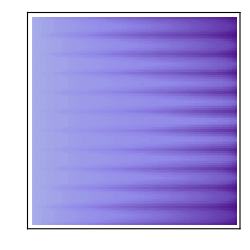
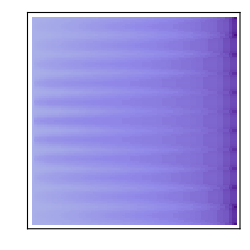
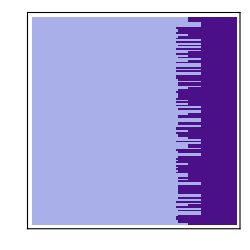
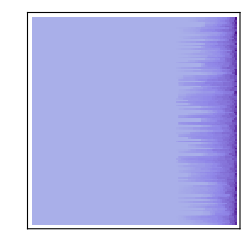
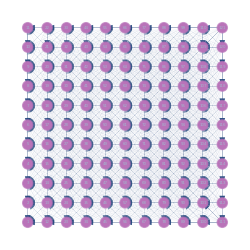
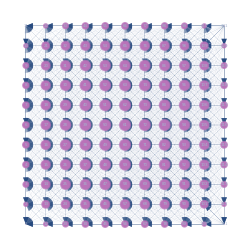
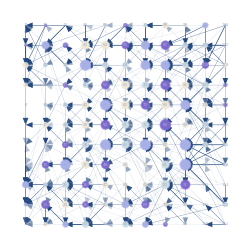
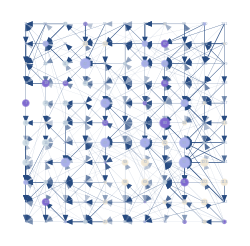
Distances Matrix | Movement Kernel | Dimensions Matrix | Applied Dimensions
-Graphics- | -Graphics- | -Graphics- | -Graphics-
 |  |  | 
Pointset | Markov Baseline | Markov Dimensional | Abs[Baseline-Dimensional]
-Graphics- | -Graphics- | -Graphics- | -Graphics-
 |  |  | 
 |  | Differences Distribution | Markov Distributions
 |  | -Graphics- | -Graphics-

./images/004ReportGrid.png

```mathematica
Grid[{
Style[#,LineBreakWithin->False]&/@{"Distances Matrix","Movement Kernel","Dimensions Matrix","Applied Dimensions"},
{matrixDistancesPlot,matrixMigrationPlot,matrixPenalizationsPlot,matrixDimensionalPlot},
{"","","",""},
Style[#,LineBreakWithin->False]&/@{"Pointset","Markov Baseline","Markov Dimensional","Abs[Baseline-Dimensional]"},
{originalMap,markovBaseline,markovDimensional,markovDimensionalDifference},
{"","","",""},
Style[#,LineBreakWithin->False]&/@{"","","Differences Distribution","Markov Distributions"},
{"","",distributionOfDifferences,markovDistributions}
}]
Export["./images/"<>StringPadLeft[networkDimension//ToString,3,"0"]<>"ReportGrid.png",%,ImageSize->5000,ImageResolution->1000]
```